## Wigner 3-j symbol

```mathematica
W[j1_,j2_,j3_,m1_,m2_,m3_]:=Module[
{t1,t2,t3,t4,t5, tmin, tmax, wigner,
factor1, factor2
},
t1=j2-m1-j3; 
t2=j1+m2-j3; 
t3=j1+j2-j3;
t4=j1-m1;
t5=j2+m2;
tmin=Max[0,Max[t1,t2]];
tmax=Min[t3,Min[t4,t5]];
wigner=0;
factor1=Sum[
(-1)^t/(Factorial[t]*Factorial[t-t1]*Factorial[t-t2]*
        Factorial[t3-t]*Factorial[t4-t]*Factorial[t5-t]),
{t,tmin, tmax,1}
];
factor2=(-1)^(j1-j2-m3)*
Sqrt[
Factorial[j1+j2-j3]*Factorial[j1-j2+j3]*
Factorial[-j1+j2+j3]/Factorial[j1+j2+j3+1]*
Factorial[j1+m1]*Factorial[j1-m1]*Factorial[j2+m2]*
Factorial[j2-m2]*Factorial[j3+m3]*Factorial[j3-m3]
];
wigner=factor1*factor2
]
```

## Definitions

```mathematica
(* Expansion coefs *)
```

```mathematica
a[m_,n_,μ_,ν_, p_]:=(-1)^(m+μ)(2p+1)(√(((n+m)! (ν+μ)! (p-m-μ)!)/((n-m)!(ν-μ)!(p+m+μ)!)))*ThreeJSymbol[{n,0},{ν,0},{p,0}]*ThreeJSymbol[{n,m},{ν,μ},{p,-m-μ}]
```

```mathematica
a2[m_,n_,μ_,ν_, p_]:=(-1)^(m+μ)(2p+1)(√(((n+m)! (ν+μ)! (p-m-μ)!)/((n-m)!(ν-μ)!(p+m+μ)!)))*W[n,ν,p,0,0,0]*
W[n,ν,p,m,μ,-m-μ]
```

```mathematica
a3[m_,n_,μ_,ν_, p_]:=Module[
{c1,c2,c3},
c1=(n+m≥ 0 )&&(n-m≥ 0 );
c2=(ν+μ≥ 0 )&&(ν-μ≥ 0 );
c3=(p-m-μ≥ 0 )&&(p+m+μ≥ 0 );
If[c1&&c2&&c3,
a[m,n,μ,ν, p], (* if indices are valid *)
0 (* else return zero*)
]
]
```

### Testing a coefficients (A-14)

```mathematica
numRep={m:>1, n:>5,μ:>1, ν:>4, p:>1 };
```

```mathematica
(a3[m,n,μ,ν,p]-(a3[m+1,n,μ,ν,p]+a3[m,n,μ+1,ν,p]))//.numRep
```

0

## Appendix A test

```mathematica
fn1[n_,m_,ν_,μ_,x_]:=LegendreP[n,m,x]*LegendreP[ν,μ,x]
```

```mathematica
fn1[2,0,2,0,1]//N
```

1.

```mathematica
fn2[n_,m_,ν_,μ_,x_]:=Sum[
LegendreP[p, m+μ,x]*a3[m,n,μ,ν, p],
{p, n+ν,Abs[n-ν], -2}
]
```

```mathematica
fn2[2,0,2,0,1]
```

1

### plot test

```mathematica
fn1[5,0,4,0,x]
```

1/64 (3-30 x^2+35 x^4) (15 x-70 x^3+63 x^5)

```mathematica
fn2[5,0,4,0,x]//FullSimplify
```

1/64 x (3-30 x^2+35 x^4) (15-70 x^2+63 x^4)

## Translation eq

### Choose the spherical function

```mathematica
Z[n_, x_]:=SphericalBesselJ[n, x];
```

### Spherical wave in initial coordinate system

```mathematica
fun1[r_, θ_, ϕ_,n_,m_]:=Z[n, k r]LegendreP[n,m, Cos[θ]]Exp[ⅈ m ϕ]//.{k:>1};
```

```mathematica
fun1[r, θ, ϕ,1,0]//.{r:>1, θ:>0, ϕ:>0}//N
```

0.301169

```mathematica
(*
	r0 - translation distance
	
*)
```

### Define translation vector

```mathematica
θ0=π/2;
ϕ0=0;
r0=1;
```

#### New coordinates in terms of old spherical coords.

```mathematica
x1[r_, θ_, ϕ_]:=r Sin[θ]Cos[ϕ]-r0 Sin[θ0]Cos[ϕ0];
y1[r_, θ_, ϕ_]:=r Sin[θ]Sin[ϕ]-r0 Sin[θ0]Sin[ϕ0];
z1[r_, θ_, ϕ_]:=r Cos[θ]-r0 Cos[θ0];
```

```mathematica
r1[r_, θ_, ϕ_]:=√(x1[r, θ, ϕ]^2+ y1[r, θ, ϕ]^2+z1[r,θ, ϕ]^2);
θ1[r_, θ_, ϕ_]:=If[r1[r,θ, ϕ]>0,ArcCos[z1[r,θ, ϕ]/r1[r,θ, ϕ]],0]; (* Avoiding singularity *)
ϕ1[r_, θ_, ϕ_]:=If[ 
x1[r, θ, ϕ]≠0&&y1[r, θ, ϕ]≠0,
ArcTan[x1[r, θ, ϕ], y1[r, θ, ϕ]],
0 (* AVOIDING PHI SINGULARITY ! *)
];
```

### Using addition theorem for spherical scalar wave function

```mathematica
fun21[r_, θ_, ϕ_,n_,m_]:=(Sum[
(-1)^μ ⅈ^(ν+p-n)(2ν+1)a3[m,n,-μ, ν, p]*
SphericalBesselJ[ν,k r1[r, θ, ϕ]]*
Z[p, k r0] LegendreP[ν,μ,Cos[θ1[r, θ, ϕ]] ]LegendreP[p,m-μ,Cos[θ0]]Exp[ⅈ(m-μ)ϕ0+ⅈ μ ϕ1[r, θ, ϕ] ],
{ν,0,5,1},
{μ, -ν, ν,1},
{p, n+ν,Abs[n-ν], -2}
]//.{k:>1})//N;
```

```mathematica
fun22[r_, θ_, ϕ_,n_,m_]:=(Sum[
(-1)^μ ⅈ^(ν+p-n)(2ν+1)a3[m,n,-μ, ν, p]*
SphericalBesselJ[ν,k r0]*
Z[p, k  r1[r, θ, ϕ]] LegendreP[ν,μ,Cos[θ0] ]LegendreP[p,m-μ,Cos[θ1[r, θ, ϕ]]]Exp[ⅈ(m-μ)ϕ1[r, θ, ϕ]+ⅈ μ ϕ0 ],
{ν,0,5,1},
{μ, -ν, ν,1},
{p, n+ν,Abs[n-ν], -2}
]//.{k:>1})//N;
```

```mathematica
fun2[r_, θ_, ϕ_,n_,m_]:=If[
r1[r, θ,ϕ]<r0,
fun21[r, θ, ϕ,n,m],
fun22[r, θ, ϕ,n,m]
]
```

## Equality test

```mathematica
(*fun2[r, θ, ϕ,n,m]*)
```

```mathematica
fun2[r0, θ0, ϕ0,4,0]//N
```

0.000379131

```mathematica
fun1[0, 0, 0,4,0]//N
```

0.

## Plots

### Spherical coordinates in terms of Cartesian

```mathematica
TH[x_,y_,z_]:=ArcCos[z/(√(x^2+y^2+z^2))]
PH[x_,y_,z_]:=ArcTan[x,y]
R[x_,y_,z_]:=√(x^2+y^2+z^2)
```

### XY plot

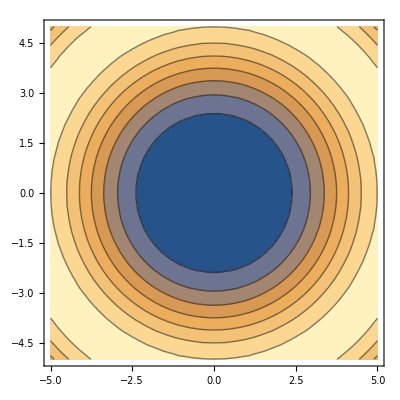

```mathematica
fun1[R[x,y,z], TH[x,y,z], PH[x,y,z],4,0]//.{z:>0}//ContourPlot[
#//Abs,
{x, -5,5},
{y, -5,5}
]&
```

```mathematica
fun2[R[x,y,z], TH[x,y,z], PH[x,y,z],4,0]//.{z:>0}//ContourPlot[
#//Abs,
{x, -5,5},
{y, -5,5}
]&
```

-Graphics-

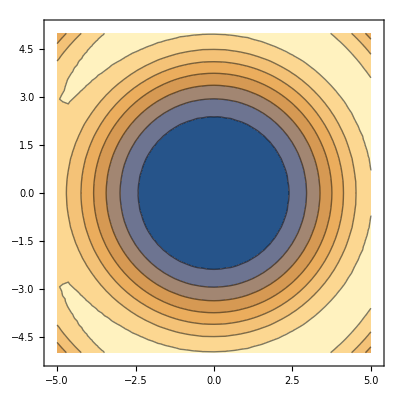

## Line along translation direction

```mathematica
fun2[x,θ0,ϕ0,4,0]
```

If[√((-1+x)^2)<1,fun21[x,π/2,0,4,0],fun22[x,π/2,0,4,0]]

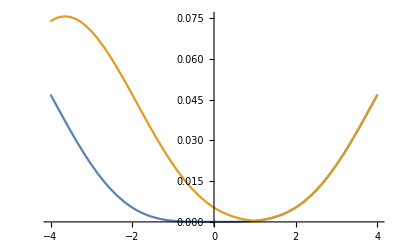

```mathematica
{fun1[x,θ0,ϕ0,4,0],
fun2[x,θ0,ϕ0,4,0]}//Plot[#, {x, -4,4}]&
```

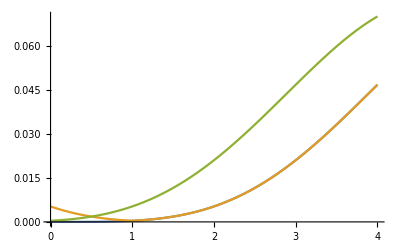

```mathematica
{fun1[x,θ0,ϕ0,4,0],
fun2[x,θ0,ϕ0,4,0],
fun1[x+1,θ0,ϕ0,4,0]}//Plot[#, {x, 0,4}]&
```

## Playground

```mathematica
(*
Sutvarkyti 
{ν,0,2,1},
{μ, -ν, ν,1},
{p, n+ν,Abs[n-ν], -2}

kitimo rezius, kad veiktu Wigner coefs
*)
```

```mathematica
fun2[r_, θ_, ϕ_,n_,m_]:=Sum[
(-1)^μ ⅈ^(ν+p-n)(2ν+1)a2[m,n,-μ, ν, p]
{ν,0,2,1},
{μ, -ν, ν,1},
{p, n+ν,Abs[n-ν], -2}
]//.{k:>1};
```